```mathematica
FSize1=30;
FSize2=24;
FontUse="Times";
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"output"];
rvout = Import["rvout.dat","Table"];
rvtest1= Table[{rvout[[i,1]]*100,rvout[[i,2]]},{i,1,Length[rvout]}];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"input\\experiment"];
exp= Import["exp_grain_size_1_6mkm.txt","Table"];
exp2= Import["exp_grain_size_40mkm.txt","Table"];
```

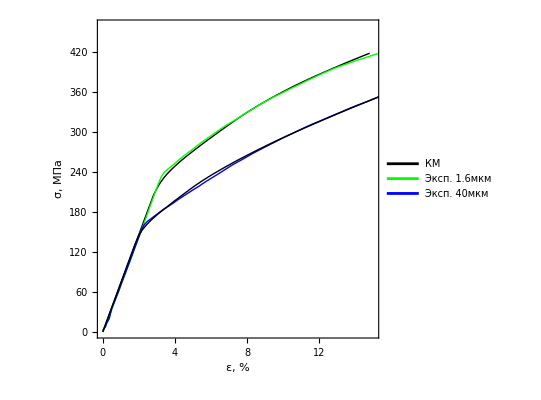

```mathematica
Img=ListLinePlot[{rvtest,exp,exp2,rvtest1} ,PlotRange-> {{0,15},All},Axes->True,Frame->True,FrameLabel->{Style["ε, %",FSize1, FontFamily->"Times"],Style["σ, МПа",FSize1, FontFamily->"Times"]},PlotLegends->Placed[{"КМ","Эксп. 1.6мкм","Эксп. 40мкм"},Above], PlotStyle->{{Black,Thick},{Green,Thick},{Blue,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1]
```

```mathematica
b=2.5 10^-10;
dg=1.6 10^-6;
√(b/dg)
```

0.0125

```mathematica
(77 10^6)/0.0125
```

6.16×10^9